# Иерархические графы. Минимизация пересечений

## Вступление

Задача данного шага состоит в сортировке вершин на каждом из слое. Порядок вершин определяет топологию конечного изображения и должен быть выбран так, чтобы минимизировать число пересечений ребер графа.

Для успешного применения иерархического подхода система изображения графов (исходные данные, визуализирующая компонента, область применения) должна удовлетворять следующим ограничениям:

1. Исходный граф должен быть ациклическим мультиграфом или «близким» к ациклическому (в этом случае, необходимо выполнить некоторую предварительную обработку исходного графа)
	2. Семантика графовой информации должна предполагать возможность построения монотонного (с одинаковой направленностью всех ребер графа) изображения
	3. Система визуализации не должна предполагать проведения только прямолинейных ребер между вершинами графа.

Предполагается, что дан ациклический направленный граф G=(V,E), где V — множество вершин, E —  множество ребер.

Известно разбиение множества вершин V на подмножества L_1, L_2,...,L_h, которые в дальнейшем будем называть слоями.

Поскольку первый этап решения задачи размещения направленных графов, связанный с разбиением вершин по уровням выполнен, то следующая задача, которую необходимо решить — это минимизация пересечений ребер, путем определения порядка вершин в ранжированных слоях.

Очевидно, что наличие пересечения двух ребер не зависит от конечных координат вершин, а зависит только от относительного положения внутри каждого уровня, таким образом, мы получаем комбинаторную задачу.

Такая задача является NP–сложной уже для графа, имеющего всего лишь два уровня. Задачу минимизации пересечений естественно сформулировать, как задачу целочисленного программирования. Точный подход к решению задачи может использоваться только для маленьких графов.

Дан k-слойный граф G=(V,E), такой что, V=V_1∪...∪V_k, V_i∩V_j=∅, 1≤i≠ j≤k. Набор ребер, E={(u,v)|u∈V_i, v∈V_(i+1), 1≤i≤k-1}. Присвоим n_i=|V_i|, m=|E|, а также примем, что N(u)={v∈V|(u,v)∈E} множество соседей вершины v. Порядок или перестановка, π_i, каждого подмножества V_i  представляет собой решение задачи минимизации пересечений, поскольку содержит относительное расположение вершин на уровне. Получаем, что мы ищем набор перестановок П={π_i|1≤i≤k}, который минимизирует количество пересечений ребер при размещении графа.

## Математическая постановка задачи целочисленного программирования

Для двухслойной задачи нам дано G=(V_1,V_2,E), необходимо найти π_1, π_2, такие, что при размещении графа мы получим минимальное количество пересечений ребер.

Модель содержит 3 вида переменных:

1. c_(i,j,k,l) обозначает пересекаются ли ребра (i,j) и (k,l), когда i<j, k<l, i<k и j ≠ l.
	2. x_(i,j) обозначает верно ли условие π_1(i)<π_1(j).
	3. y_(i,j) обозначает верно ли условие π_2(i)<π_2(j)

Для решения задачи целочисленного программирования будем искать минимум целевой функции:

L(c;x;y)→min

Выбор целевой функции обусловлен главной целью оптимизации — минимизация пересечений ребер графа при размещении на плоскости.

Обозначенной цели удовлетворяет следующий вид целевой функции:

(L(c;x;y)=∑)_((i,j),(k,l)∈E)^c_(i,j,k,l)→min

Ограничения задачи целочисленного программирования:

1. -c_(i,j,k,l)≤y_(j,l)-x_(i,k)≤c_(i,j,k,l)      (i, j), (k, l) ∈E, j<l

Если c_(i,j,k,l)=0, тогда неравенство определяет, что порядок вершин i и k, должен быть такой же, как у вершин j и l; соответственно, если ребра (i,j) и (k,l)  пересекаются, тогда y_(j,l)-x_(i,k)={-1,1}, определяя c_(i,j,k,l)=1.

2. 1-c_(i,j,k,l)≤y_(l,j)+x_(i,k)≤1+c_(i,j,k,l)   (i,j),(k,l)∈E, j>l

Поскольку не существует переменной y_(j,l), j>l, тогда в неравенстве делаем замену y_(j,l)=1-y_(l,j). Ниже представлен рисунок, соответствующий ограничениям (1) и (2).

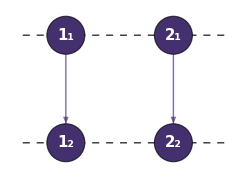
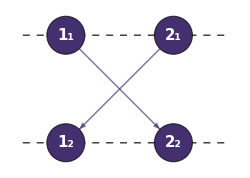
-Graphics-
c_(1,1,2,2)≤y_(1,2)-x_(1,2)≤c_(1,1,2,2) | -Graphics-
1-c_(1,2,2,1)≤y_(1,2)+x_(1,2)≤1+c_(1,2,2,1)

3. 0≤x_(i,j)+x_(j,k)-x_(i,k)≤1                  1≤i<j<k≤n_1

Выполнение транзитивности для 3–х вершин первого слоя.

4. 0≤y_(i,j)+y_(j,k)-y_(i,k)≤1                  1≤i<j<k≤n_2

Выполнение транзитивности для 3–х вершин второго слоя.

Все переменные — булевы.

В многослойной задаче нам дано G=(V_1,...,V_k,E) необходимо найти π_1,..., π_k, такие, что при размещении графа мы получим минимальное количество пересечений ребер.

## Эвристические методы

#### 1. Метод барицентров

На практике наиболее широко используются линейные алгоритмы, основанные на методе барицентров. Координата вершины v∈V_2 определяется как среднее арифметическое координат всех её связей с уровня V_1.

Input: ориентированный граф G=(V_1,V_2,E), V_1 — фиксированные вершины первого уровня, V_2 — фиксированные вершины второго уровня, π_1 — перестановка вершин первого уровня;
Output: перестановка π_2;
1   x_v=π_1(v),v∈V_1 ;
2   repeat
3   	foreach u∈V_2 do
4   		arg(u)→ 1/(deg(u))∑_(v∈N(u)), где N(u)={v|{u,v}∈E}
5   	π_2=sort(avg(u)|u∈V_2);

π_2=sort(avg(u)|u∈V_2) — функция sort сортирует вершины по возрастанию значения arg.

Если после перестановки координаты каких-либо вершин совпадают, то они разносятся на минимальное расстояние при произвольном порядке.

Следующий интерактивный модуль поможет разобраться с работой метода барицентров для нечетной итерации на примере двухслойных графов. Модуль позволяет генерировать двухслойные графы и получать подробную информацию по работе эвристического метода для данного примера (значения коэффициентов и их расчет, а также информация по подсчету количества пересечений)

#### 2. Метод медиан и его базовые вариации

Самая распространенная модификация метода барицентров — метод медиан, где вместо среднего арифметического используется координата среднего соседа  x_1 с предыдущего уровня, т.е. если u_1,u_2,...,u_m ∈ V_1 — вершины смежные v, причем x_1(u_1)<x_1(u_2)<...<x_1(u_m), то координата x_2(v)=med(v) определяется как x_1(u_avg), где avg=⌊m/2⌋.

В случае, когда med(v)=med(u) и v имеет нечетную степень, а u — четную , то v ставится перед u; если же четность степеней совпадает, то порядок выбирается произвольно. Данная эвристика является линейной.

Развитие метода средних медиан, отличающееся от него только в случае вершин с четной степенью, большей двух. В этом случае взвешенная медиана определяется как

vmed(u)=(x_1(v_(j/2))×right + x_1(v_(j/2 + 1))×left)/(left + right),где left=x_1(v_(j/2)) - x_1(v_1), и right=x_1(v_j) - x_1(v_(j/2+1))

Такая стратегия сдвигает вершины к той стороне, где ее соседи располагаются наиболее плотно.

#### 3. Применение метода барицентров и медиан

Методы медиан, барицентров и взвешенных медиан являются итерационными. При этом направление обхода графа зависит от четности итерации, если итерация нечетная обход осуществляется от головной вершины к листьям, если четная — от листьев к головной вершине. После проведения каждой итерации определяется текущее число пересечений ребер графа. Если количество пересечений в результате выполнения итерации сокращается, то полученный порядок вершин записывается как «текущий лучший». Следовательно, во время расчета необходимо использовать функцию подсчета количества пересечений на слое. При подсчете пересечений исследуются все пары ребер на данном уровне.

Input: ориентированный граф G=(V,E), и множество начальных перестановок вершин на слоях П_0
Output: набор перестановок П_return;
1  procedure ordering()
2 	П = П_0;
3 	П_return = П;
4 	for i = 0 to Max_iterations do
5 		П = heuristic(П,i);
6		if crossing(П) < crossing(П_return) then
7			П_return = П;
8	end
9	return П_return;
10  end

Следовательно, во время расчета необходимо использовать функцию crossing, которая в качестве исходных данных использует порядок вершин, а на выходе дает число пересечений ребер графа.

При подсчете пересечений исследуются все пары ребер на двухслойном подграфе, которые представляет собой соседние слои графа. Ниже представлен алгоритм исследования двух пар ребер (u_1,v_1) и (u_2,v_2), где вершины u_1  и u_2  принадлежат слою i, а вершины v_1  и v_2 — слою i+1. Перестановку уровня i хранит π_i  (вызов π_i(u)  возвращает позицию вершины u), аналогично, перестановку слоя i+1 хранит π_(i+1).

Input: ориентированный граф G=(V,E), 
	перестановка вершин на i-ом слое  π_i, 
	перестановка вершин на i+1–м слое  π_(i+1), 
	пара ребер (u_1,v_1) и (u_2,v_2)
Output: пересекаются ли ребра (u_1,v_1) и (u_2,v_2) при данных перестановках вершин на слоях
1 procedure is_crossing(u_1,v_1,u_2,v_2)
2	if π_i (u_1)=π_i (u_2 ) ∨ π_(i+1) (v_1)=π_(i+1) (v_2 ) then
3		return 0;
4		else
5		return π_i (u_1)<π_i (u_2) ⊕ π_(i+1)(v_1)<π_(i+1) (v_2 );
6 end
Здесь ⊕ означает «исключающее или», т.е. оператор XOR.